# Правила замены и локальные подстановки

Локальное правило

```mathematica
x->4
```

x→4

```mathematica
x
```

x

```mathematica
?x
```

Global`x

```mathematica
p=4;
?p
```

Global`p

p=4

```mathematica
√x+x^2
```

√x+x^2

```mathematica
√p+p^2
```

18

Подстановка локального правила

```mathematica
r=x->4
```

x→4

```mathematica
r
```

x→4

```mathematica
√x+x^2/.r
```

18

```mathematica
x^2+Sin[x]/.x->√y
```

y+Sin[√y]

Замена по списку

```mathematica
x^2+Sin[y]/.{x->√z,y->4}
```

z+Sin[4]

Взаимные замены

```mathematica
√y+x^2/.{x->y,y->x}
```

√x+y^2

```mathematica
√y+x^2/.x->y/.y->x
```

√x+x^2

```mathematica
√y+x^2/.{x->y,y->z}
```

y^2+√z

Замена с повторением

```mathematica
√y+x^2//.{x->y,y->z}
```

√z+z^2

x=1 (⇔Set[x,1]    — глобальное правило, после создания применяется во всех вычислениях автоматически)
x→1 (⇔Rule[x,1] — локальное правило)
x^2/.x→1 (⇔ ReplaceAll[x^2,x→1] — применение локального правила)
x^2+y/.{x→y,y→4}    (однократное применение списка правил)

x^2+y//.{x→y,y→4} (⇔ ReplaceRepeated[…] — полное применение списка правил)
x:>1 (⇔RuleDelayed[x,1] — задание локального правила с отложенным вычислением правой части)

```mathematica
√x+x^2 √y/.√t_:>Sin[t]
```

Sin[x]+x^2 Sin[y]

Замена операторов

```mathematica
a+b/.Plus->Times
```

a b

ReplaceAll[ ] vs Apply[ ]

```mathematica
Times@@(a+b)
```

a b

```mathematica
(a+b)^2/.Plus->Times
```

a^2 b^2

```mathematica
Times@@((a+b)^2)
```

2 (a+b)

```mathematica
Apply[Times,√(a+√b)]
```

1/2 (a+√b)

```mathematica
√(a+√b)/.Power->Times
```

1/2 (a+b/2)

# Выражения сравнения

```mathematica
x==4
```

x==4

```mathematica
?x
```

Global`x

```mathematica
3==4
```

False

```mathematica
2 2==4
```

True

a==b (⇔a==b⇔Equal[a,b] — выражение равенства)
a≠b (⇔a!=b⇔Unequal[a,b] — выражение неравенства)

a≥b (⇔a<=b⇔GreaterEqual[a,b])
a≤b (⇔a>=b⇔LessEqual[a,b])
a>b (⇔Greater[a,b])
a<b (⇔Less[a,b])

!！!
== — равенство (Equal[])
	= —  задание глобального правила (Set[])

# Аналитические решения алгебраических уравнений

Уравнения

```mathematica
x^2+x==4
```

x+x^2==4

```mathematica
Solve[x^2+x==4]
```

{{x→1/2 (-1-√17)},{x→1/2 (-1+√17)}}

```mathematica
Solve[x^2+x==-4]
```

{{x→1/2 (-1-ⅈ √15)},{x→1/2 (-1+ⅈ √15)}}

```mathematica
Solve[x^2+√x==4]
```

{{x→-1/(2 √(3/(16+(8219/2-(3 √49233)/2)^(1/3)+(1/2 (8219+3 √49233))^(1/3))))-1/2 √(32/3-1/3 (8219/2-(3 √49233)/2)^(1/3)-1/3 (1/2 (8219+3 √49233))^(1/3)-2 √(3/(16+(8219/2-(3 √49233)/2)^(1/3)+(1/2 (8219+3 √49233))^(1/3))))},{x→-1/(2 √(3/(16+(8219/2-(3 √49233)/2)^(1/3)+(1/2 (8219+3 √49233))^(1/3))))+1/2 √(32/3-1/3 (8219/2-(3 √49233)/2)^(1/3)-1/3 (1/2 (8219+3 √49233))^(1/3)-2 √(3/(16+(8219/2-(3 √49233)/2)^(1/3)+(1/2 (8219+3 √49233))^(1/3))))},{x→1/(2 √(3/(16+(8219/2-(3 √49233)/2)^(1/3)+(1/2 (8219+3 √49233))^(1/3))))-1/2 √(32/3-1/3 (8219/2-(3 √49233)/2)^(1/3)-1/3 (1/2 (8219+3 √49233))^(1/3)+2 √(3/(16+(8219/2-(3 √49233)/2)^(1/3)+(1/2 (8219+3 √49233))^(1/3))))}}

Неявные неизвестные

```mathematica
Solve[a x^2+x==4]
```

{{a→(4-x)/x^2}}

```mathematica
(*Solve[a x+b==0]
TreeForm[a x+b==0]*)
```

Явные неизвестные

```mathematica
Solve[a x^2+x==4,x]
```

{{x→(-1-√(1+16 a))/(2 a)},{x→(-1+√(1+16 a))/(2 a)}}

Системы уравнений

```mathematica
Solve[{x+y==4,y^2==a},{x,y}]
```

{{x→4+√a,y→-√a},{x→4-√a,y→√a}}

Использование решений

```mathematica
sol=Solve[{x+y==4,y^2==a},{x,y}]
```

{{x→4+√a,y→-√a},{x→4-√a,y→√a}}

```mathematica
x/.sol
```

{4+√a,4-√a}

```mathematica
sol⟦;;,1,2⟧
```

{4+√a,4-√a}

```mathematica
sol⟦1,1,2⟧
```

4+√a

```mathematica
sol⟦1,;;,2⟧
```

{4+√a,-√a}

```mathematica
x+4y/.sol
```

{4-3 √a,4+3 √a}

Отбор решений

```mathematica
sol=Solve[{x^2+x==1}]
```

{{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

```mathematica
sol⟦1⟧
x/.sol⟦1⟧
```

{x→1/2 (-1-√5)}

1/2 (-1-√5)

```mathematica
Solve[{x^2+x==1,x>0}]
```

{{x→1/2 (-1+√5)}}

```mathematica
Solve[{x^2+√y==2,y^2==1},{x,y}]
```

{{x→-√(2-ⅈ),y→-1},{x→√(2-ⅈ),y→-1},{x→-1,y→1},{x→1,y→1}}

```mathematica
Solve[{x^2+√y==2,y^2==1,x∈Reals},{x,y}]
```

{{x→-1,y→1},{x→1,y→1}}

```mathematica
Solve[{x^2+√y==2,y^2==1,Im[x]==0},{x,y}]
```

{{x→-1,y→1},{x→1,y→1}}

# *Комплексные числа

ⅈ==ii==I==√-1

```mathematica
√-1
```

ⅈ

```mathematica
ⅈ^2
```

-1

```mathematica
Exp[ⅈ π]
```

-1

```mathematica
(a+ⅈ b)(b+c ⅈ)
```

(a+ⅈ b) (b+ⅈ c)

```mathematica
(a+ⅈ b)(b+c ⅈ)//ComplexExpand
```

a b-b c+ⅈ (b^2+a c)

```mathematica
Re[(a+ⅈ b)(b+c ⅈ)]//ComplexExpand
```

a b-b c

```mathematica
Im[(a+ⅈ b)(b+c ⅈ)]//ComplexExpand
```

b^2+a c

```mathematica
ReIm[(a+ⅈ b)(b+c ⅈ)]//ComplexExpand
```

{a b-b c,b^2+a c}

ReIm[#]=={Re[#],Im[#]}

```mathematica
Re[2+ⅈ]
Im[2+ⅈ]
```

2

1

```mathematica
ReIm[2+ⅈ]
```

{2,1}

# Численные решения алгебраических уравнений

```mathematica
Solve[4Cos[x]==x,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[4 Cos[x]==x,x]

```mathematica
NSolve[4Cos[x]==x,x,Reals]
```

{{x→-3.5953},{x→-2.13333},{x→1.25235}}

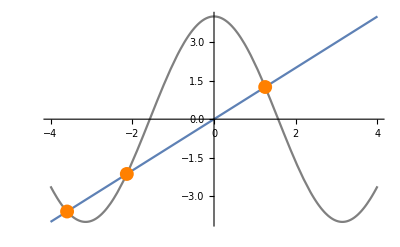

```mathematica
sol=NSolve[4Cos[x]==x,x,Reals];
Show[{
Plot[{x,4Cos[x]},{x,-4,4},PlotStyle->{Automatic,Gray}],
ListPlot[{x,4Cos[x]}/.sol,PlotStyle->Directive[Orange,PointSize->0.025]]
}]
```

Быстрый поиск отдельного корня

```mathematica
FindRoot[4Cos[x]==x,{x,1}]
```

{x→1.25235}

```mathematica
FindRoot[4Cos[x]==x,{x,-4}]
FindRoot[4Cos[x]==x,{x,-2}]
FindRoot[4Cos[x]==x,{x,1}]
```

{x→-3.5953}

{x→-2.13333}

{x→1.25235}

```mathematica
NSolve[x==Tan[x],x,Reals]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[x==Tan[x],x,ℝ]

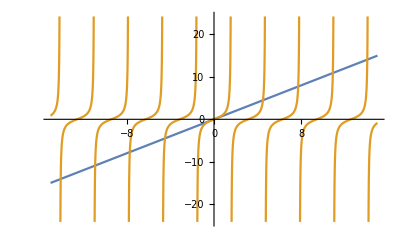

```mathematica
Plot[{x,Tan[x]},{x,-15,15}]
```

```mathematica
FindRoot[{x==Tan[x]},{x,4}]
```

{x→4.49341}

```mathematica
FindRoot[{x==Tan[x]},{x,10}]
```

{x→10.9041}

Solve[] — решение алгебраических систем аналитическими методами
NSolve[] — решение алгебраических систем численными методами
FindRoot[] — быстрый поиск отдельного корня по начальному приближению

```mathematica
Solve[x^2==2,x]
Solve[x^2==2,x]//N
NSolve[x^2==2,x]
```

{{x→-√2},{x→√2}}

{{x→-1.41421},{x→1.41421}}

{{x→-1.41421},{x→1.41421}}

```mathematica
Solve[4Cos[x]==x,x]//N
NSolve[4Cos[x]==x,x,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[4. Cos[x]==x,x]

{{x→-3.5953},{x→-2.13333},{x→1.25235}}

# *Примеры

## Обращение замены координат

Исходная замена ({x, y} -> {x1, y1}) :

```mathematica
transform={x->x1+2y1,y->3x1-y1}
```

{x→x1+2 y1,y→3 x1-y1}

Система уравнений

```mathematica
transform/.Rule->Equal
```

{x==x1+2 y1,y==3 x1-y1}

Обратная замена ({x1, y1} -> {x, y}) :

```mathematica
Solve[transform/.Rule->Equal,{x1,y1}]
```

{{x1→1/7 (x+2 y),y1→1/7 (3 x-y)}}

* +автоматическое определение неизвестных:

```mathematica
newcoords=Cases[transform⟦;;,2⟧,_Symbol,All]//DeleteDuplicates
```

{x1,y1}

```mathematica
Solve[transform/.Rule->Equal,newcoords]
```

{{x1→1/7 (x+2 y),y1→1/7 (3 x-y)}}

## Замена внутренних параметров выражения

```mathematica
CustomPlot[expression_,range_,options___]:=
Plot[expression,range,PlotStyle->{
color/.{options}/.(color->Green (* цвет по умолчанию *))
}];
```

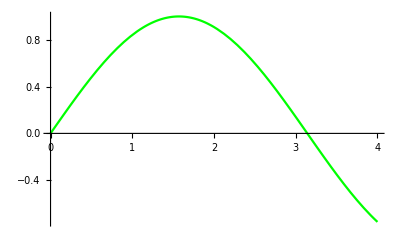

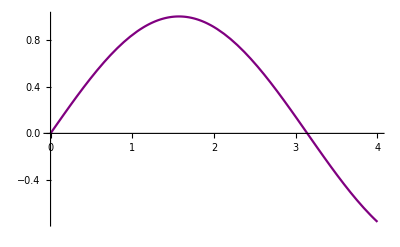

```mathematica
CustomPlot[Sin[x],{x,0,4}]
CustomPlot[Sin[x],{x,0,4},color->Purple]
```

Последовательность замен при вычислении без аргумента options:

```mathematica
color/.{} (* color -> color *)
color/.{}/.(color->Green) (* color /. color -> Green ⇒ Green *)
```

color

RGBColor[0, 1, 0]

Последовательность замен при вычислении с аргументом options :

```mathematica
color/.{color -> Purple} (* color -> Purple *)
color/.{color -> Purple}/.(color->Green) (* Purple /. color -> Green ⇒ Purple *)
```

RGBColor[0.5, 0, 0.5]

RGBColor[0.5, 0, 0.5]